```mathematica
l2nest = Import["/Users/mcarnright/ANN/l2.csv","CSV"]
```

{{0.498089,0.500413,0.500408,0.499942,0.499632,0.500015,0.500018,0.499983,0.497541,0.500351,0.500624,0.499952,0.491308,0.501374,0.500571,0.499851,0.494884,0.500835,0.500596,0.499542,0.49872,0.500084,0.500483,0.49987,0.498399,0.500321,0.500007,0.499756,0.492291,0.500976,0.500103,0.499753,0.494695,0.500456,0.500138,0.499947,0.497639,0.5001,0.500238,0.499478,0.494039,0.500193,0.501036,0.49982,0.493971,0.500456,0.500545,0.499584,0.495941,0.500347,0.500893,0.499553,0.490408,0.500139,0.500193,0.499922,0.495856,0.50007,0.500388,0.49996,0.495479,0.500189,0.500723,0.499449,0.494041,0.50032,0.500487,0.4994,0.492802,0.501121,0.500198,0.499352,0.495257,0.500358,0.500445,0.499563,0.495195,0.500405,0.501502,0.499753,0.495856,0.500065,0.500953,0.499633,0.493022,0.500277,0.501105,0.499627,0.496795,0.500876,0.500433,0.499847,0.496089,0.500598,0.500134,0.499834,0.495362,0.500002,0.500414,0.499932,0.497354,0.500102,0.500178,0.499835,0.495981,0.500282,0.500651,0.49937,0.495046,0.500093,0.500031,0.499349,0.493551,0.500156,0.500922,0.499515,0.491493,0.500844,0.500053,0.499213,0.493576,0.500278,0.500714,0.499542,0.495171,0.500286,0.500253,0.499022,0.494337,0.500421,0.500977,0.499418,0.492173,0.500022,0.500228,0.499894,0.497416,0.500453,0.500131,0.499893,0.496741,0.500836,0.500292,0.499575,0.498234,0.500504,0.500265,0.499983,0.498716,0.500222,0.500145,0.499883,0.495572,0.500375,0.500603,0.499985,0.498466,0.500038,0.500147,0.499652,0.491685,0.500664,0.500011,0.499997,0.49141,0.500067,0.500109,0.499328,0.496498,0.500337,0.500234,0.499954,0.494719,0.500206,0.50022,0.499817,0.495304,0.501628,0.500011,0.499886,0.497202,0.500291,0.500203,0.499924,0.494431,0.500348,0.50053,0.499941,0.497495,0.500747,0.500661,0.499796,0.496813,0.500412,0.501228,0.499753,0.494043,0.500592,0.500753,0.499747,0.495922,0.50042,0.500224,0.499964,0.494515,0.500177,0.50021,0.499858,0.498509,0.500053,0.500008,0.499687,0.499208,0.500143,0.500039,0.49999,0.497886,0.500044,0.500365,0.499887,0.49907,0.500067,0.500389,0.499964,0.492882,0.500231,0.500567,0.499097,0.499038,0.500359,0.50002,0.49996,0.494338,0.500233,0.5001,0.499954,0.499152,0.500111,0.500387,0.499926,0.494198,0.50079,0.501977,0.499687,0.497482,0.500194,0.500548,0.499889,0.495582,0.500052,0.500728,0.499541,0.490682,0.501102,0.501287,0.499611,0.497493,0.500764,0.500111,0.49978,0.495841,0.501938,0.500226,0.499961,0.497801,0.500697,0.500036,0.4997,0.497883,0.500058,0.500186,0.499858,0.494551,0.500872,0.500446,0.49965,0.498671,0.500591,0.500606,0.499986,0.498378,0.500066,0.500007,0.49985,0.494745,0.501671,0.500775,0.499969,0.494739,0.50059,0.500875,0.499353,0.496945,0.500977,0.500426,0.49999,0.496532,0.500269,0.500274,0.499993,0.495457,0.500879,0.500509,0.499807,0.498132,0.500381,0.500327,0.499875,0.493822,0.500465,0.50113,0.499661,0.498055,0.500032,0.500076,0.499741,0.493766,0.500247,0.500859,0.499735,0.491066,0.501154,0.500492,0.499236,0.495054,0.500317,0.500275,0.499836,0.495909,0.500173,0.500704,0.49949,0.498208,0.500001,0.500188,0.499806,0.498689,0.500216,0.500118,0.499967,0.495062,0.500394,0.500004,0.499707,0.493474,0.500268,0.500861,0.499533,0.491209,0.500821,0.500394,0.499802,0.497233,0.500171,0.500695,0.499897,0.494936,0.500024,0.501591,0.499972,0.496167,0.500573,0.500287,0.499968,0.496443,0.50023,0.500876,0.499603,0.497366,0.500405,0.500081,0.499498,0.492424,0.500485,0.500373,0.499295,0.49436,0.500698,0.500936,0.499848,0.495948,0.500001,0.500518,0.499988,0.490021,0.500825,0.500165,0.498691,0.495003,0.500948,0.500603,0.499405,0.490978,0.500375,0.500122,0.499013,0.495261,0.500556,0.50045,0.499927,0.496582,0.500377,0.500507,0.499354,0.493458,0.501214,0.500128,0.498895,0.496443,0.500815,0.500308,0.49986,0.496954,0.500521,0.500034,0.499927,0.495841,0.500224,0.50024,0.499887,0.489921,0.501547,0.50056,0.499598,0.497602,0.500503,0.500772,0.499941,0.492182,0.500289,0.501565,0.499043,0.489224,0.500382,0.502236,0.499272,0.495012,0.500135,0.500145,0.499421,0.492409,0.501837,0.500006,0.499726,0.497548,0.500438,0.500166,0.499989,0.49114,0.500268,0.501076,0.498873,0.483952,0.500659,0.501188,0.499687,0.499056,0.500104,0.500083,0.499942,0.494133,0.500081,0.501196,0.498771,0.493732,0.500787,0.50165,0.499781,0.494871,0.50087,0.500229,0.499474,0.495266,0.500348,0.501963,0.499824,0.489874,0.500113,0.500793,0.499755,0.495093,0.500012,0.501432,0.499964,0.497968,0.50021,0.500276,0.499582,0.49366,0.500012,0.500282,0.498995,0.489161,0.500601,0.500898,0.499246,0.490355,0.501558,0.500402,0.499352,0.495862,0.50125,0.50003,0.499701,0.492759,0.50127,0.501391,0.499906,0.491331,0.501647,0.50131,0.499826,0.497559,0.500763,0.500926,0.499921,0.498919,0.500103,0.500361,0.499747,0.49664,0.50016,0.500182,0.499416,0.493923,0.500354,0.500275,0.499286,0.493115,0.502183,0.50126,0.499827,0.499183,0.500028,0.50015,0.499757,0.493167,0.500349,0.501137,0.499865,0.492042,0.501584,0.501124,0.4996,0.497054,0.500129,0.500431,0.499646,0.497517,0.500071,0.500079,0.499358,0.488223,0.501104,0.500467,0.499709,0.49609,0.500344,0.500466,0.499742,0.4987,0.500139,0.500263,0.499945,0.499172,0.500079,0.500156,0.499987,0.494508,0.500949,0.500914,0.499955,0.49071,0.500857,0.50135,0.499977,0.490146,0.501134,0.500506,0.499737,0.493238,0.500143,0.500949,0.499808,0.493782,0.500012,0.501206,0.499893,0.490636,0.500099,0.500232,0.498817,0.497076,0.50024,0.500817,0.499962,0.496842,0.500591,0.500048,0.499841,0.498908,0.500305,0.500178,0.499973,0.491973,0.500566,0.501042,0.499906,0.496396,0.500069,0.500347,0.499708,0.496123,0.500008,0.500427,0.499981,0.494679,0.501108,0.501998,0.499902,0.495814,0.500623,0.500111,0.499825,0.497592,0.500488,0.500098,0.499991,0.495423,0.500236,0.500476,0.499718,0.499419,0.500399,0.500027,0.499966,0.491895,0.500338,0.500478,0.498883,0.493834,0.500174,0.502186,0.499814,0.495956,0.50009,0.500671,0.499782,0.495501,0.500026,0.50178,0.499751,0.494657,0.500019,0.500658,0.499862,0.497729,0.5006,0.5001,0.499738,0.49685,0.500134,0.500237,0.499898,0.495483,0.500476,0.500192,0.499071,0.49366,0.500059,0.50011,0.499832,0.494571,0.500376,0.500603,0.499916,0.498115,0.500298,0.500029,0.499633,0.497111,0.500337,0.500293,0.499993,0.497629,0.500174,0.500005,0.499887,0.497599,0.50051,0.500341,0.499639,0.495727,0.500332,0.500321,0.499734,0.495587,0.500079,0.500529,0.499386,0.496685,0.500023,0.500192,0.499339,0.493323,0.500427,0.500109,0.499647,0.496919,0.500076,0.500757,0.499456,0.498966,0.500156,0.500023,0.499802,0.492593,0.500314,0.500351,0.499283,0.496427,0.500094,0.500432,0.499868,0.494499,0.500875,0.501206,0.49992,0.498,0.500018,0.500177,0.499931,0.497414,0.500572,0.500204,0.499957,0.49872,0.500301,0.500097,0.499864,0.499423,0.500244,0.50001,0.499989,0.498675,0.500175,0.50025,0.499772,0.496045,0.500459,0.500867,0.499869,0.495752,0.500433,0.500831,0.499744,0.493111,0.500562,0.501794,0.499827,0.496949,0.500599,0.500049,0.499872,0.49382,0.501432,0.500055,0.499774,0.493906,0.500838,0.500255,0.499198,0.494206,0.500482,0.500556,0.499847,0.492915,0.50015,0.500586,0.499376,0.494117,0.500409,0.500551,0.499474,0.496678,0.501294,0.500589,0.49996,0.493248,0.500799,0.500499,0.499781,0.495369,0.501501,0.500438,0.499814,0.49776,0.500133,0.500033,0.499774,0.498203,0.500069,0.500265,0.49971,0.496352,0.500425,0.500243,0.499859,0.493226,0.500189,0.500066,0.498364,0.497972,0.500151,0.500051,0.499926,0.498117,0.500264,0.500618,0.49985,0.493595,0.500209,0.50099,0.499565,0.49716,0.500006,0.500243,0.499425,0.495167,0.500396,0.501961,0.499819,0.49358,0.500298,0.502332,0.49996,0.492653,0.500711,0.500099,0.499022,0.495971,0.501192,0.500069,0.499934,0.499239,0.500013,0.50033,0.499858,0.495195,0.500132,0.500039,0.49994,0.49595,0.501265,0.50049,0.499659,0.497048,0.50013,0.500059,0.498851,0.495675,0.501009,0.500847,0.499878,0.497214,0.500172,0.500403,0.49966,0.496754,0.50068,0.500141,0.499881,0.495554,0.500237,0.500916,0.499415,0.493471,0.500015,0.500048,0.499499,0.498057,0.500745,0.500051,0.499889,0.491895,0.502024,0.500742,0.499952,0.49052,0.500573,0.502556,0.499793,0.492845,0.500095,0.500947,0.499418,0.489364,0.500684,0.500785,0.498925,0.493655,0.500376,0.501011,0.499371,0.494243,0.501817,0.500539,0.499811,0.489603,0.501183,0.500346,0.499808,0.491532,0.500582,0.500256,0.499337,0.496101,0.500469,0.500311,0.499994,0.495936,0.500105,0.500278,0.499904,0.495174,0.500642,0.500604,0.499256,0.496608,0.500456,0.500639,0.499966,0.499008,0.500284,0.500096,0.499907,0.489981,0.500036,0.500645,0.499965,0.493258,0.500548,0.500949,0.499805,0.496033,0.500001,0.500391,0.499839,0.493473,0.502568,0.500765,0.499534,0.495253,0.500825,0.501056,0.499891,0.490084,0.500526,0.500132,0.499727,0.492369,0.500399,0.501405,0.499555,0.495015,0.500109,0.500589,0.499465,0.494327,0.500772,0.50077,0.499588,0.498431,0.500005,0.500187,0.499927,0.49771,0.500134,0.500392,0.499915,0.496939,0.500043,0.501568,0.499846,0.499509,0.50009,0.500014,0.499997,0.490753,0.500051,0.500072,0.497733,0.495393,0.500339,0.501559,0.499393,0.498322,0.500254,0.500875,0.499933,0.493092,0.500699,0.500544,0.499976,0.495967,0.500181,0.500579,0.499926,0.496376,0.501921,0.500283,0.499837,0.493601,0.501085,0.50003,0.4988,0.494507,0.501696,0.500643,0.499876,0.493794,0.501475,0.500704,0.499485,0.497736,0.500083,0.50058,0.499872,0.497431,0.500189,0.500672,0.49983,0.496915,0.500104,0.500501,0.499987,0.494626,0.500214,0.501267,0.499349,0.498868,0.500054,0.500002,0.499941,0.496284,0.500111,0.500218,0.499926,0.498236,0.500327,0.500165,0.499662,0.499418,0.500022,0.500009,0.499938,0.498687,0.500032,0.500099,0.499598,0.499283,0.500264,0.50002,0.499999,0.492698,0.500161,0.500706,0.499259,0.499248,0.500002,0.500052,0.499959,0.496851,0.500116,0.500389,0.499452,0.491513,0.500247,0.501926,0.499361}}

```mathematica
l2= l2nest[[1]]
```

{0.498089,0.500413,0.500408,0.499942,0.499632,0.500015,0.500018,0.499983,0.497541,0.500351,0.500624,0.499952,0.491308,0.501374,0.500571,0.499851,0.494884,0.500835,0.500596,0.499542,0.49872,0.500084,0.500483,0.49987,0.498399,0.500321,0.500007,0.499756,0.492291,0.500976,0.500103,0.499753,0.494695,0.500456,0.500138,0.499947,0.497639,0.5001,0.500238,0.499478,0.494039,0.500193,0.501036,0.49982,0.493971,0.500456,0.500545,0.499584,0.495941,0.500347,0.500893,0.499553,0.490408,0.500139,0.500193,0.499922,0.495856,0.50007,0.500388,0.49996,0.495479,0.500189,0.500723,0.499449,0.494041,0.50032,0.500487,0.4994,0.492802,0.501121,0.500198,0.499352,0.495257,0.500358,0.500445,0.499563,0.495195,0.500405,0.501502,0.499753,0.495856,0.500065,0.500953,0.499633,0.493022,0.500277,0.501105,0.499627,0.496795,0.500876,0.500433,0.499847,0.496089,0.500598,0.500134,0.499834,0.495362,0.500002,0.500414,0.499932,0.497354,0.500102,0.500178,0.499835,0.495981,0.500282,0.500651,0.49937,0.495046,0.500093,0.500031,0.499349,0.493551,0.500156,0.500922,0.499515,0.491493,0.500844,0.500053,0.499213,0.493576,0.500278,0.500714,0.499542,0.495171,0.500286,0.500253,0.499022,0.494337,0.500421,0.500977,0.499418,0.492173,0.500022,0.500228,0.499894,0.497416,0.500453,0.500131,0.499893,0.496741,0.500836,0.500292,0.499575,0.498234,0.500504,0.500265,0.499983,0.498716,0.500222,0.500145,0.499883,0.495572,0.500375,0.500603,0.499985,0.498466,0.500038,0.500147,0.499652,0.491685,0.500664,0.500011,0.499997,0.49141,0.500067,0.500109,0.499328,0.496498,0.500337,0.500234,0.499954,0.494719,0.500206,0.50022,0.499817,0.495304,0.501628,0.500011,0.499886,0.497202,0.500291,0.500203,0.499924,0.494431,0.500348,0.50053,0.499941,0.497495,0.500747,0.500661,0.499796,0.496813,0.500412,0.501228,0.499753,0.494043,0.500592,0.500753,0.499747,0.495922,0.50042,0.500224,0.499964,0.494515,0.500177,0.50021,0.499858,0.498509,0.500053,0.500008,0.499687,0.499208,0.500143,0.500039,0.49999,0.497886,0.500044,0.500365,0.499887,0.49907,0.500067,0.500389,0.499964,0.492882,0.500231,0.500567,0.499097,0.499038,0.500359,0.50002,0.49996,0.494338,0.500233,0.5001,0.499954,0.499152,0.500111,0.500387,0.499926,0.494198,0.50079,0.501977,0.499687,0.497482,0.500194,0.500548,0.499889,0.495582,0.500052,0.500728,0.499541,0.490682,0.501102,0.501287,0.499611,0.497493,0.500764,0.500111,0.49978,0.495841,0.501938,0.500226,0.499961,0.497801,0.500697,0.500036,0.4997,0.497883,0.500058,0.500186,0.499858,0.494551,0.500872,0.500446,0.49965,0.498671,0.500591,0.500606,0.499986,0.498378,0.500066,0.500007,0.49985,0.494745,0.501671,0.500775,0.499969,0.494739,0.50059,0.500875,0.499353,0.496945,0.500977,0.500426,0.49999,0.496532,0.500269,0.500274,0.499993,0.495457,0.500879,0.500509,0.499807,0.498132,0.500381,0.500327,0.499875,0.493822,0.500465,0.50113,0.499661,0.498055,0.500032,0.500076,0.499741,0.493766,0.500247,0.500859,0.499735,0.491066,0.501154,0.500492,0.499236,0.495054,0.500317,0.500275,0.499836,0.495909,0.500173,0.500704,0.49949,0.498208,0.500001,0.500188,0.499806,0.498689,0.500216,0.500118,0.499967,0.495062,0.500394,0.500004,0.499707,0.493474,0.500268,0.500861,0.499533,0.491209,0.500821,0.500394,0.499802,0.497233,0.500171,0.500695,0.499897,0.494936,0.500024,0.501591,0.499972,0.496167,0.500573,0.500287,0.499968,0.496443,0.50023,0.500876,0.499603,0.497366,0.500405,0.500081,0.499498,0.492424,0.500485,0.500373,0.499295,0.49436,0.500698,0.500936,0.499848,0.495948,0.500001,0.500518,0.499988,0.490021,0.500825,0.500165,0.498691,0.495003,0.500948,0.500603,0.499405,0.490978,0.500375,0.500122,0.499013,0.495261,0.500556,0.50045,0.499927,0.496582,0.500377,0.500507,0.499354,0.493458,0.501214,0.500128,0.498895,0.496443,0.500815,0.500308,0.49986,0.496954,0.500521,0.500034,0.499927,0.495841,0.500224,0.50024,0.499887,0.489921,0.501547,0.50056,0.499598,0.497602,0.500503,0.500772,0.499941,0.492182,0.500289,0.501565,0.499043,0.489224,0.500382,0.502236,0.499272,0.495012,0.500135,0.500145,0.499421,0.492409,0.501837,0.500006,0.499726,0.497548,0.500438,0.500166,0.499989,0.49114,0.500268,0.501076,0.498873,0.483952,0.500659,0.501188,0.499687,0.499056,0.500104,0.500083,0.499942,0.494133,0.500081,0.501196,0.498771,0.493732,0.500787,0.50165,0.499781,0.494871,0.50087,0.500229,0.499474,0.495266,0.500348,0.501963,0.499824,0.489874,0.500113,0.500793,0.499755,0.495093,0.500012,0.501432,0.499964,0.497968,0.50021,0.500276,0.499582,0.49366,0.500012,0.500282,0.498995,0.489161,0.500601,0.500898,0.499246,0.490355,0.501558,0.500402,0.499352,0.495862,0.50125,0.50003,0.499701,0.492759,0.50127,0.501391,0.499906,0.491331,0.501647,0.50131,0.499826,0.497559,0.500763,0.500926,0.499921,0.498919,0.500103,0.500361,0.499747,0.49664,0.50016,0.500182,0.499416,0.493923,0.500354,0.500275,0.499286,0.493115,0.502183,0.50126,0.499827,0.499183,0.500028,0.50015,0.499757,0.493167,0.500349,0.501137,0.499865,0.492042,0.501584,0.501124,0.4996,0.497054,0.500129,0.500431,0.499646,0.497517,0.500071,0.500079,0.499358,0.488223,0.501104,0.500467,0.499709,0.49609,0.500344,0.500466,0.499742,0.4987,0.500139,0.500263,0.499945,0.499172,0.500079,0.500156,0.499987,0.494508,0.500949,0.500914,0.499955,0.49071,0.500857,0.50135,0.499977,0.490146,0.501134,0.500506,0.499737,0.493238,0.500143,0.500949,0.499808,0.493782,0.500012,0.501206,0.499893,0.490636,0.500099,0.500232,0.498817,0.497076,0.50024,0.500817,0.499962,0.496842,0.500591,0.500048,0.499841,0.498908,0.500305,0.500178,0.499973,0.491973,0.500566,0.501042,0.499906,0.496396,0.500069,0.500347,0.499708,0.496123,0.500008,0.500427,0.499981,0.494679,0.501108,0.501998,0.499902,0.495814,0.500623,0.500111,0.499825,0.497592,0.500488,0.500098,0.499991,0.495423,0.500236,0.500476,0.499718,0.499419,0.500399,0.500027,0.499966,0.491895,0.500338,0.500478,0.498883,0.493834,0.500174,0.502186,0.499814,0.495956,0.50009,0.500671,0.499782,0.495501,0.500026,0.50178,0.499751,0.494657,0.500019,0.500658,0.499862,0.497729,0.5006,0.5001,0.499738,0.49685,0.500134,0.500237,0.499898,0.495483,0.500476,0.500192,0.499071,0.49366,0.500059,0.50011,0.499832,0.494571,0.500376,0.500603,0.499916,0.498115,0.500298,0.500029,0.499633,0.497111,0.500337,0.500293,0.499993,0.497629,0.500174,0.500005,0.499887,0.497599,0.50051,0.500341,0.499639,0.495727,0.500332,0.500321,0.499734,0.495587,0.500079,0.500529,0.499386,0.496685,0.500023,0.500192,0.499339,0.493323,0.500427,0.500109,0.499647,0.496919,0.500076,0.500757,0.499456,0.498966,0.500156,0.500023,0.499802,0.492593,0.500314,0.500351,0.499283,0.496427,0.500094,0.500432,0.499868,0.494499,0.500875,0.501206,0.49992,0.498,0.500018,0.500177,0.499931,0.497414,0.500572,0.500204,0.499957,0.49872,0.500301,0.500097,0.499864,0.499423,0.500244,0.50001,0.499989,0.498675,0.500175,0.50025,0.499772,0.496045,0.500459,0.500867,0.499869,0.495752,0.500433,0.500831,0.499744,0.493111,0.500562,0.501794,0.499827,0.496949,0.500599,0.500049,0.499872,0.49382,0.501432,0.500055,0.499774,0.493906,0.500838,0.500255,0.499198,0.494206,0.500482,0.500556,0.499847,0.492915,0.50015,0.500586,0.499376,0.494117,0.500409,0.500551,0.499474,0.496678,0.501294,0.500589,0.49996,0.493248,0.500799,0.500499,0.499781,0.495369,0.501501,0.500438,0.499814,0.49776,0.500133,0.500033,0.499774,0.498203,0.500069,0.500265,0.49971,0.496352,0.500425,0.500243,0.499859,0.493226,0.500189,0.500066,0.498364,0.497972,0.500151,0.500051,0.499926,0.498117,0.500264,0.500618,0.49985,0.493595,0.500209,0.50099,0.499565,0.49716,0.500006,0.500243,0.499425,0.495167,0.500396,0.501961,0.499819,0.49358,0.500298,0.502332,0.49996,0.492653,0.500711,0.500099,0.499022,0.495971,0.501192,0.500069,0.499934,0.499239,0.500013,0.50033,0.499858,0.495195,0.500132,0.500039,0.49994,0.49595,0.501265,0.50049,0.499659,0.497048,0.50013,0.500059,0.498851,0.495675,0.501009,0.500847,0.499878,0.497214,0.500172,0.500403,0.49966,0.496754,0.50068,0.500141,0.499881,0.495554,0.500237,0.500916,0.499415,0.493471,0.500015,0.500048,0.499499,0.498057,0.500745,0.500051,0.499889,0.491895,0.502024,0.500742,0.499952,0.49052,0.500573,0.502556,0.499793,0.492845,0.500095,0.500947,0.499418,0.489364,0.500684,0.500785,0.498925,0.493655,0.500376,0.501011,0.499371,0.494243,0.501817,0.500539,0.499811,0.489603,0.501183,0.500346,0.499808,0.491532,0.500582,0.500256,0.499337,0.496101,0.500469,0.500311,0.499994,0.495936,0.500105,0.500278,0.499904,0.495174,0.500642,0.500604,0.499256,0.496608,0.500456,0.500639,0.499966,0.499008,0.500284,0.500096,0.499907,0.489981,0.500036,0.500645,0.499965,0.493258,0.500548,0.500949,0.499805,0.496033,0.500001,0.500391,0.499839,0.493473,0.502568,0.500765,0.499534,0.495253,0.500825,0.501056,0.499891,0.490084,0.500526,0.500132,0.499727,0.492369,0.500399,0.501405,0.499555,0.495015,0.500109,0.500589,0.499465,0.494327,0.500772,0.50077,0.499588,0.498431,0.500005,0.500187,0.499927,0.49771,0.500134,0.500392,0.499915,0.496939,0.500043,0.501568,0.499846,0.499509,0.50009,0.500014,0.499997,0.490753,0.500051,0.500072,0.497733,0.495393,0.500339,0.501559,0.499393,0.498322,0.500254,0.500875,0.499933,0.493092,0.500699,0.500544,0.499976,0.495967,0.500181,0.500579,0.499926,0.496376,0.501921,0.500283,0.499837,0.493601,0.501085,0.50003,0.4988,0.494507,0.501696,0.500643,0.499876,0.493794,0.501475,0.500704,0.499485,0.497736,0.500083,0.50058,0.499872,0.497431,0.500189,0.500672,0.49983,0.496915,0.500104,0.500501,0.499987,0.494626,0.500214,0.501267,0.499349,0.498868,0.500054,0.500002,0.499941,0.496284,0.500111,0.500218,0.499926,0.498236,0.500327,0.500165,0.499662,0.499418,0.500022,0.500009,0.499938,0.498687,0.500032,0.500099,0.499598,0.499283,0.500264,0.50002,0.499999,0.492698,0.500161,0.500706,0.499259,0.499248,0.500002,0.500052,0.499959,0.496851,0.500116,0.500389,0.499452,0.491513,0.500247,0.501926,0.499361}

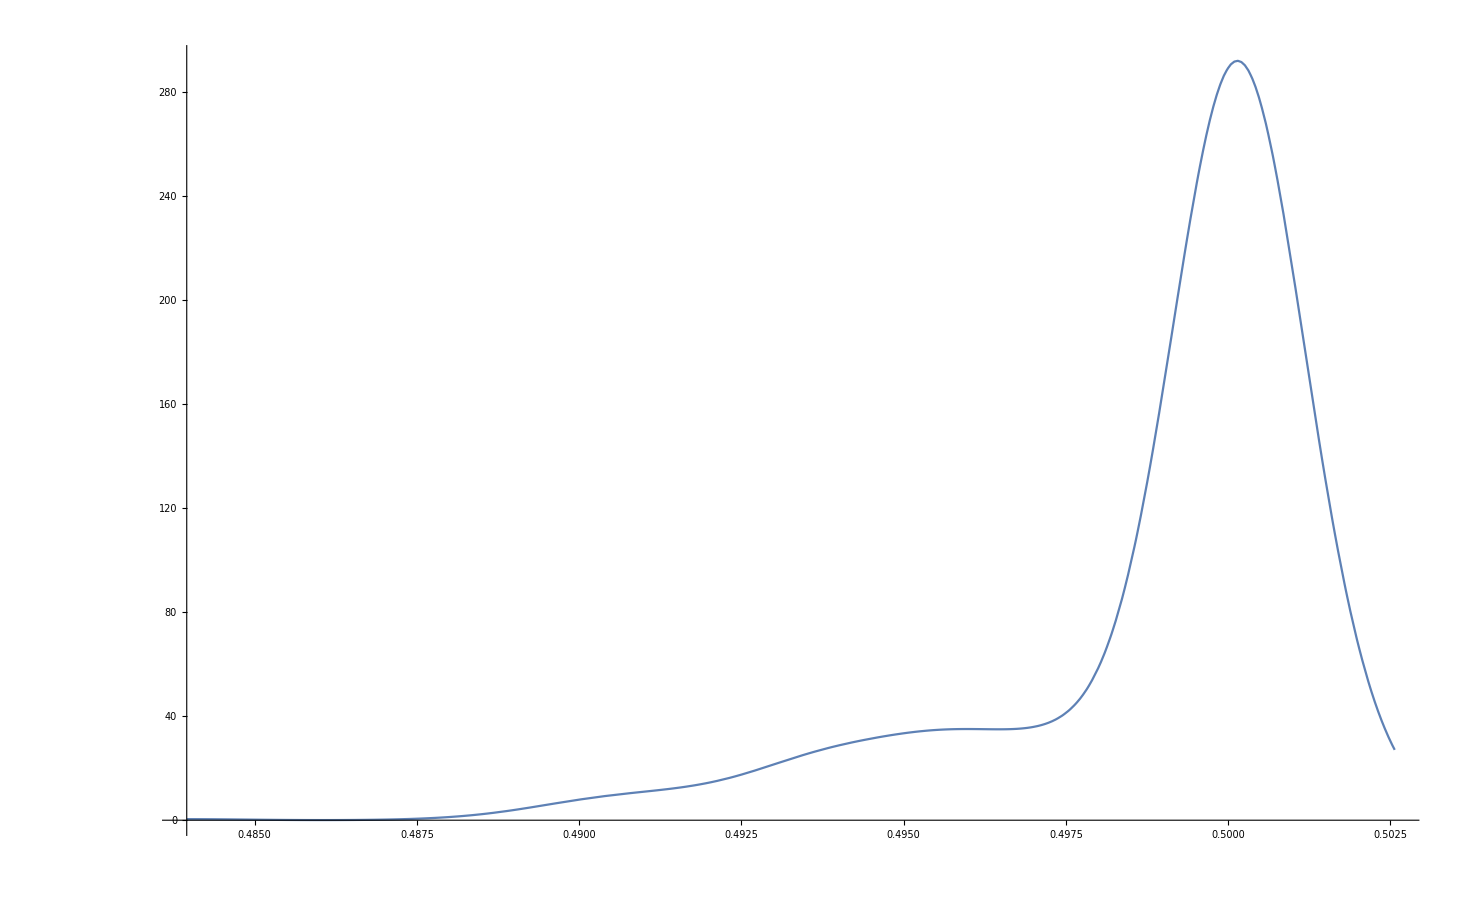

```mathematica
Plot[Evaluate@PDF[SmoothKernelDistribution[l2,.0009],x],{x,Min[l2],Max[l2]}]
```

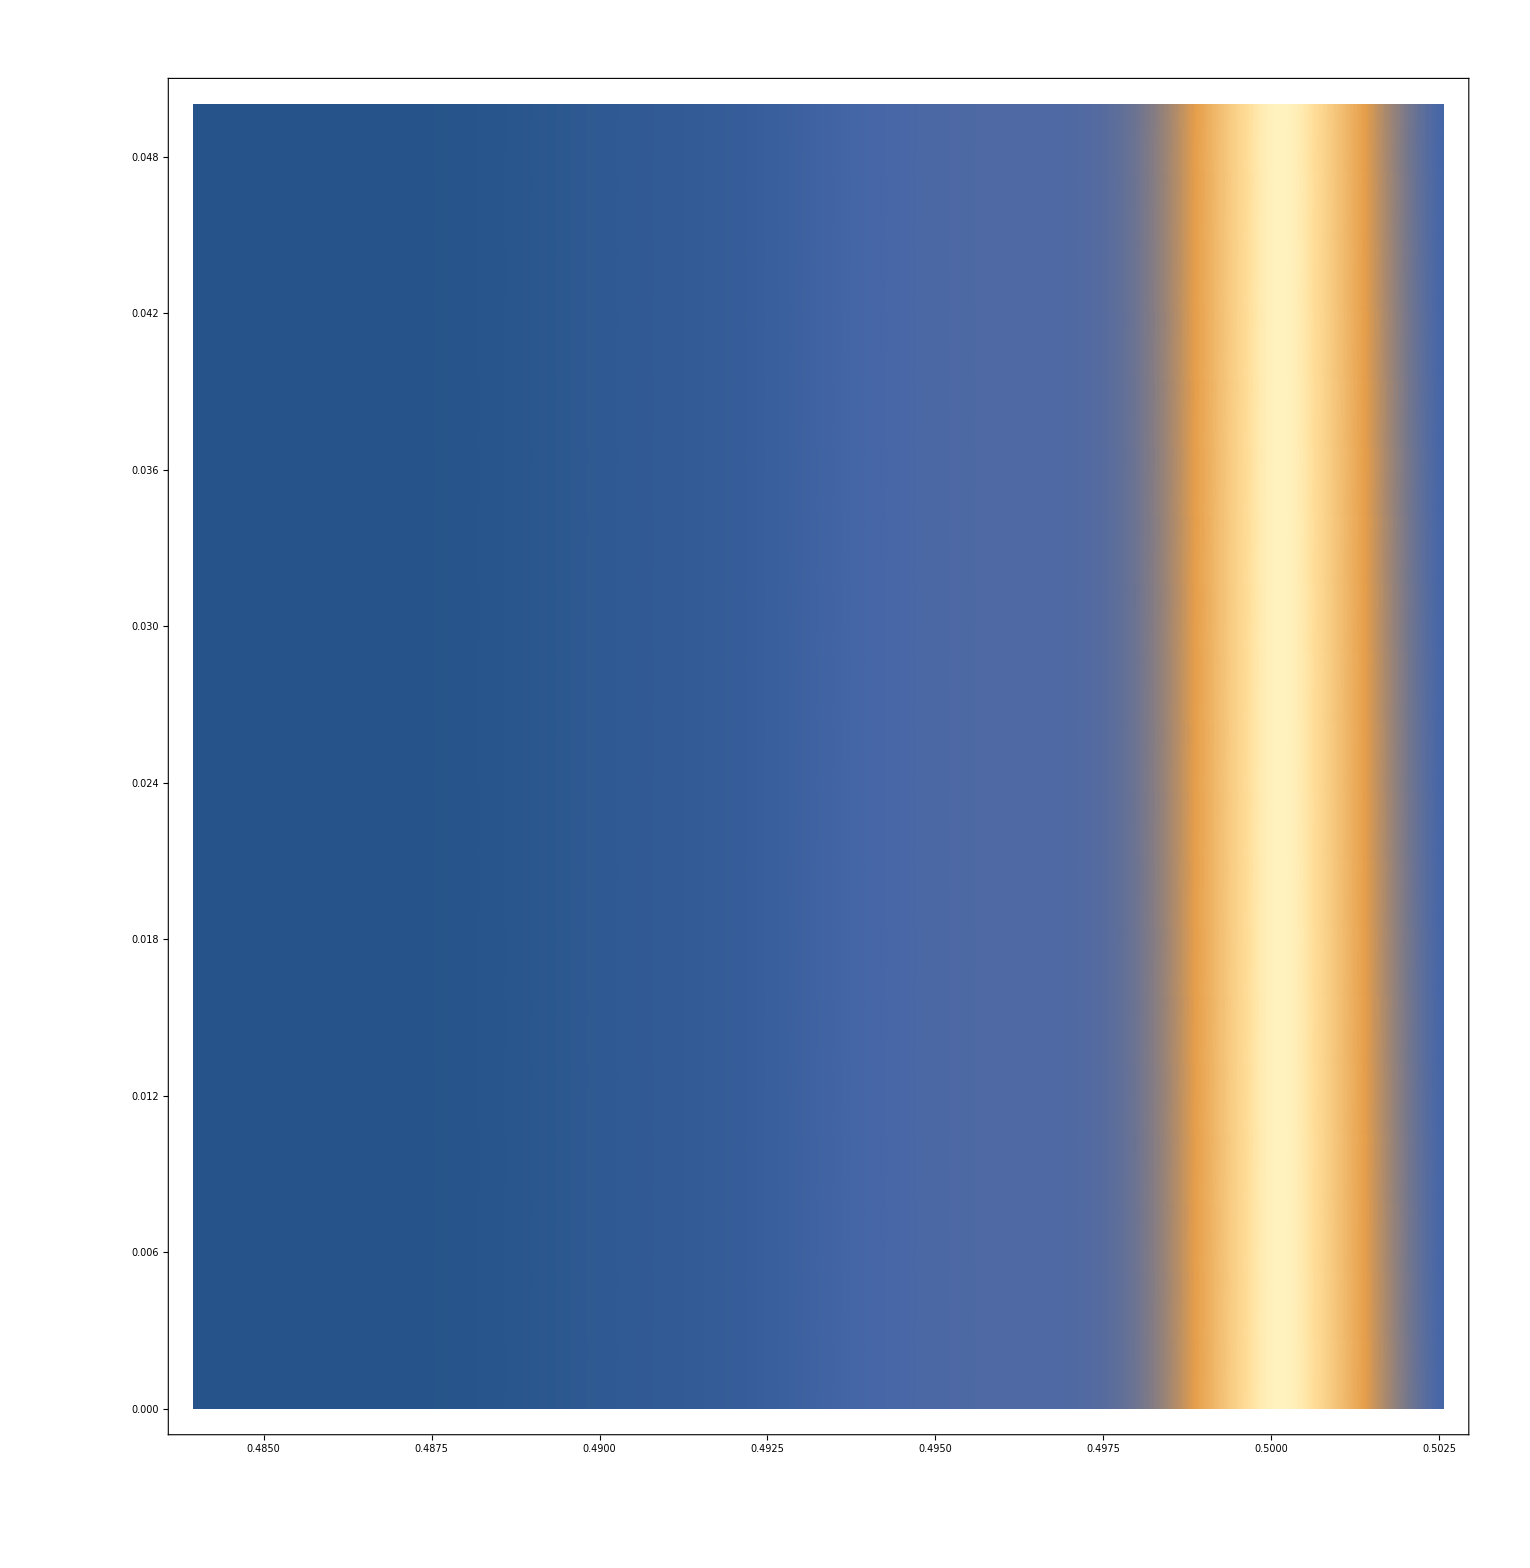

```mathematica
DensityPlot[Evaluate[{PDF[SmoothKernelDistribution[l2,.0009],x],0}],{x,Min[l2],Max[l2]},{y,0,.05},AspectRatio->Automatic,PlotPoints->{1000,20}]
```

```mathematica
syn0nest = Import["/Users/mcarnright/ANN/syn0.csv","CSV"]


syn0= syn0nest[[1]]
```

{{1.21073,1.48791,1.1335,1.36931,1.16823,1.46489,1.04662,1.26716,1.34972,1.04945,0.995932,0.740981,0.785886,1.3822,0.60833,1.2296,0.962275,1.33487,1.11711,1.44364,1.25376,0.653202,1.22211,0.635664,1.43748,0.814412,1.39751,0.787323,1.35767,0.666489,19640,1.06008,1.25925,1.10689,1.4682,0.768625,1.15584,1.42494,1.19293,1.46609,1.22352,1.07166,0.854409,1.32237,1.03946,1.46,0.852549,1.384,0.94826,0.652129,1.01482,0.993724,1.39271,1.30979,0.611074,1.45717,0.777624,0.856669,1.36306,0.852433,1.43535}}
 |  |  |  |

{1.21073,1.48791,1.1335,1.36931,1.16823,1.46489,1.04662,1.26716,1.34972,1.04945,0.995932,0.740981,0.785886,1.3822,0.60833,1.2296,0.962275,1.33487,1.11711,1.44364,1.25376,0.653202,1.22211,0.635664,1.43748,0.814412,1.39751,0.787323,1.35767,0.666489,19640,1.06008,1.25925,1.10689,1.4682,0.768625,1.15584,1.42494,1.19293,1.46609,1.22352,1.07166,0.854409,1.32237,1.03946,1.46,0.852549,1.384,0.94826,0.652129,1.01482,0.993724,1.39271,1.30979,0.611074,1.45717,0.777624,0.856669,1.36306,0.852433,1.43535}
 |  |  |  |

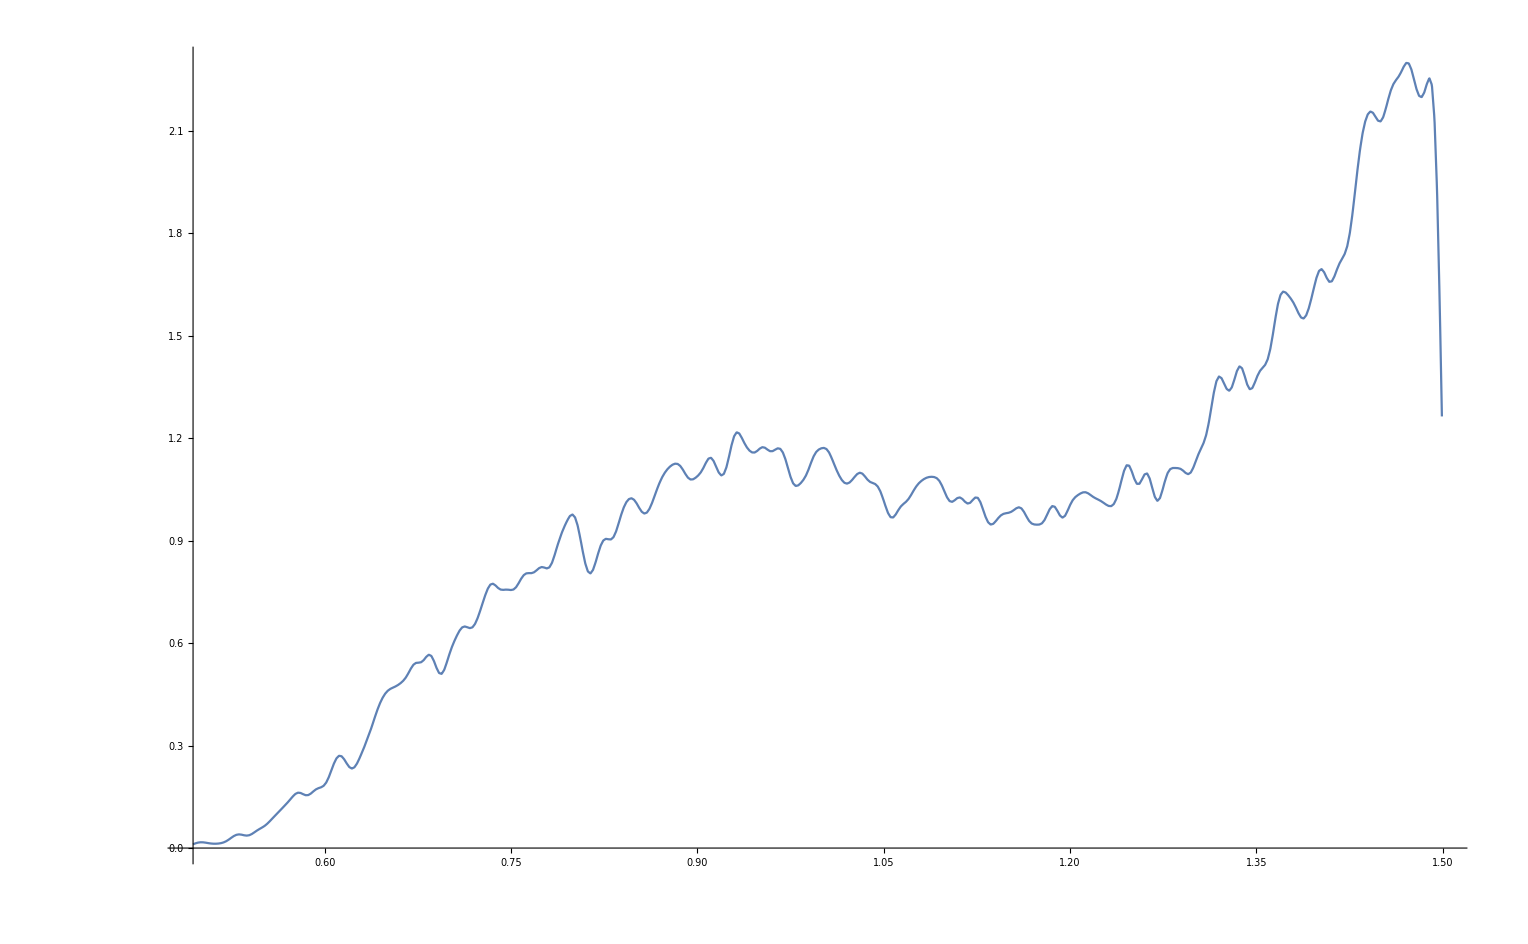

```mathematica
Plot[Evaluate@PDF[SmoothKernelDistribution[syn0,.005],x],{x,Min[syn0],Max[syn0]}]
```

```mathematica
DensityPlot[Evaluate[{PDF[SmoothKernelDistribution[syn0,.005],x],0}],{x,Min[syn0],Max[syn0]},{y,0,.01},AspectRatio->Automatic,PlotPoints->{1000,20}]
```

-Graphics-

```mathematica
syn1nest = Import["/Users/mcarnright/ANN/syn1.csv","CSV"]
syn1 = syn1nest[[1]]
```

{{-1.37052,1.31389,-0.951058,0.908843,0.819404,-0.873087,-0.525001,0.451423,-0.407856,0.381931,0.403169,-0.474624,0.373152,-0.424974,0.758716,-0.902974,-1.45223,1.42422,0.350809,-0.387422,0.0408933,-0.0416334,0.839608,-0.914896,-1.33799,1.2602,1.27402,-1.2976,1.20588,9904,-1.26219,-1.30457,1.24935,-1.20818,1.12039,0.59928,-0.626852,0.169917,-0.180292,1.31275,-1.44993,-0.559354,0.510928,0.532884,-0.629378,-1.48048,1.31758,-0.995763,0.959232,1.0949,-1.17832,-1.13692,1.05263,-0.983239,0.943973,0.60142,-0.669357,0.816822,-0.886962}}
 |  |  |  |

{-1.37052,1.31389,-0.951058,0.908843,0.819404,-0.873087,-0.525001,0.451423,-0.407856,0.381931,0.403169,-0.474624,0.373152,-0.424974,0.758716,-0.902974,-1.45223,1.42422,0.350809,-0.387422,0.0408933,-0.0416334,0.839608,-0.914896,-1.33799,1.2602,1.27402,-1.2976,1.20588,9904,-1.26219,-1.30457,1.24935,-1.20818,1.12039,0.59928,-0.626852,0.169917,-0.180292,1.31275,-1.44993,-0.559354,0.510928,0.532884,-0.629378,-1.48048,1.31758,-0.995763,0.959232,1.0949,-1.17832,-1.13692,1.05263,-0.983239,0.943973,0.60142,-0.669357,0.816822,-0.886962}
 |  |  |  |

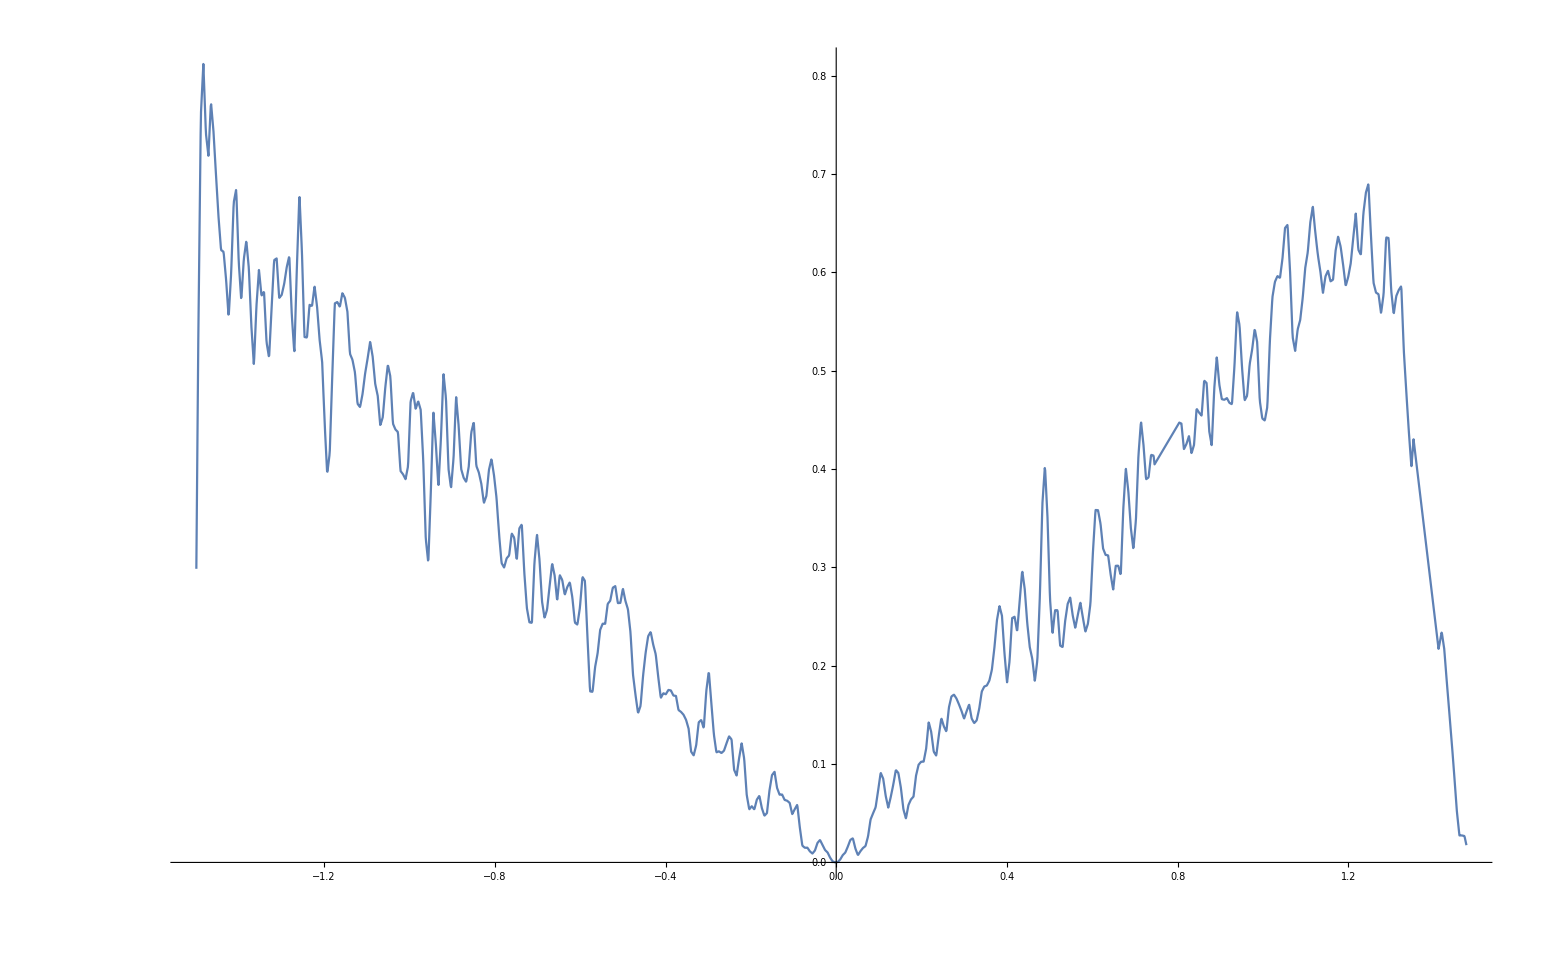

```mathematica
Plot[Evaluate@PDF[SmoothKernelDistribution[syn1,.005],x],{x,Min[syn1],Max[syn1]}]
```

```mathematica
DensityPlot[Evaluate[{PDF[SmoothKernelDistribution[syn1,.005],x],0}],{x,Min[syn1],Max[syn1]},{y,0,.05},AspectRatio->Automatic,PlotPoints->{1000,20}]
```

-Graphics-